```mathematica
(* This module creates a K-M curve using the given filename *)
dir=NotebookDirectory[]<>"runData/";
makeSurvivalCurve[filename_]:=Module[
{data,patients,time,ci,S},
data=Import[dir<>filename,"Data"];
patients = data[[4;;]]; (* The first 3 lines contain parameter info *)
time={};
(* We now loop over all patients and look to see when progression occurs (we add large number to cure so it will never show progression in the K-M curve). *)
For[n=1,n≤ Length[patients],n++,
If[patients[[n,2]]=="cure",AppendTo[time,patients[[n,1]]+10000],AppendTo[time,patients[[n,1]]]]];
ci=0&/@Range[Length[time]];
S=SurvivalModelFit[EventData[time,ci]];
{time,ci,patients,S}
]
```

```mathematica
Figure 3a: Parameter variance
```

3

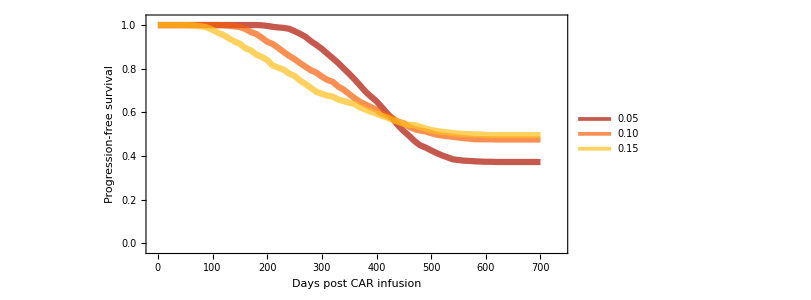

```mathematica
nStart=1;
nEnd=3;
nFiles = nEnd-nStart+1
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n,Break[]],{n,1,100}]*)
sigmaSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nFiles];
Tf=700;
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["SolarColors"][#]]}}&/@{0.15,0.5,0.9};
fig3a=ListPlot[
Table[{#,sigmaSurvivalCurves[[l]][#]}&/@Range[0,Tf,10],{l,1,nFiles}],
Joined->True,
PlotRange->{{-0.01,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[{"0.05","0.10","0.15","0.2"},{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]
```

```mathematica
Export[NotebookDirectory[]<>"varyingSigma.pdf",fig3a,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingSigma.pdf

```mathematica
Figure 3b: Impact of tumor growth rate
```

9

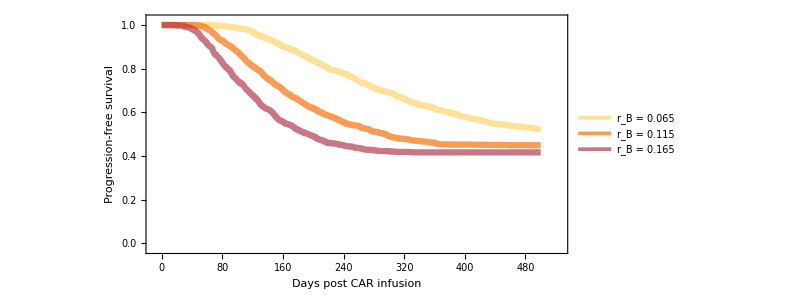

```mathematica
nStart=4;
nEnd=12;
nFiles = nEnd-nStart+1
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
rBsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
Tf=500;
mylist={1,3,5};
legend="r_B = "<>ToString[0.065+0.025#]&/@Range[0,10];
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["SolarColors"][#]]}}&/@{0.15,0.5,0.9};
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["SunsetColors"][#]]}}&/@{0.8,0.5,0.3};
fig3b=ListPlot[
Table[{#,rBsurvivalCurves[[l]][#]}&/@Range[0,Tf,Tf/1000.],{l,mylist}],
Joined->True,
PlotRange->{{-0.02,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[legend[[#]]&/@mylist,{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]
```

```mathematica
Export[NotebookDirectory[]<>"varyingTumorGrowthRate.pdf",fig3b,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingTumorGrowthRate.pdf

```mathematica
Figure 3c: Impact of chemo-depletion on survival
```

```mathematica
nStart=13;
nEnd=20;
nFiles = nEnd-nStart+1;
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
WTsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

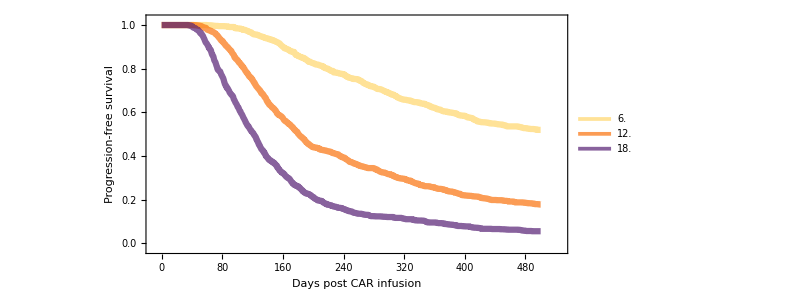

```mathematica
Tf=500;
legend={6.0,12.0,18.0};
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["SunsetColors"][#]]}}&/@{0.8,0.5,0.15};
fig3c=ListPlot[
Table[{#,WTsurvivalCurves[[l]][#]}&/@Range[0,Tf,Tf/1000.],{l,{1,2,3}}],
Joined->True,
PlotRange->{{-0.02,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[legend,{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]
```

```mathematica
Export[NotebookDirectory[]<>"varyingInitialWT.pdf",fig3c,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingInitialWT.pdf

```mathematica
Figure 3d: Impact of memory fraction on survival
```

```mathematica
nStart=21;
nEnd=31;
nFiles = nEnd-nStart+1;
date="2019-11-20";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
memFracSurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

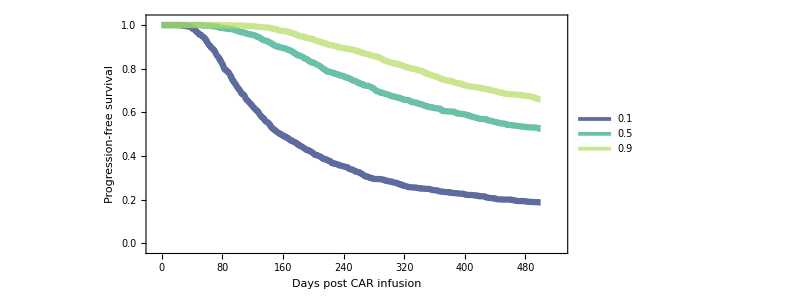

```mathematica
Tf=500;
legend=ToString[#]&/@Range[0,1,0.1];
mylist={2,6,10};
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["BlueGreenYellow"][#]]}}&/@{0.1,0.5,0.9};
fig3d=ListPlot[
Table[{#,memFracSurvivalCurves[[l]][#]}&/@Range[0,Tf,Tf/1000.],{l,mylist}],
Joined->True,
PlotRange->{{-0.02,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[legend[[#]]&/@mylist,{0.85,0.85}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]
```

```mathematica
Export[NotebookDirectory[]<>"varyingInitialCARmemory.pdf",fig3d,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingInitialCARmemory.pdf

```mathematica
Figure 3d: Impact of initial tumor size on survival
```

```mathematica
nStart=1;
nEnd=9;
nFiles = nEnd-nStart+1;
date="2019-11-21";
(*Do[If[FileExistsQ[dir<>"outputData_"<>ToString[n]<>"_"<>date<>".txt"],nFiles=n-nStart+1,Break[]],{n,nStart,100}]*)
B0survivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
```

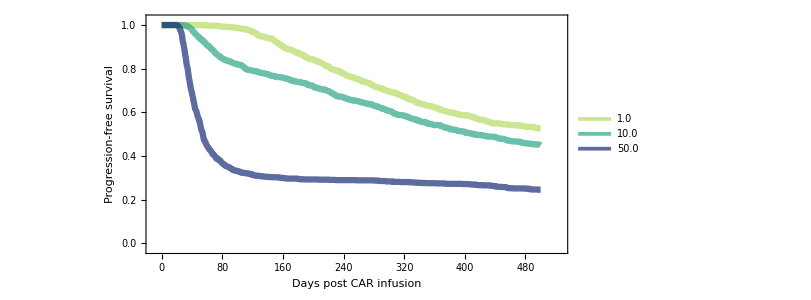

```mathematica
Tf=500;
legend={"0.01","0.1","1.0","2.0","5.0","10.0","20.0","50.0",100.0};
mylist={3,6,8};
colorList={{Thickness[0.0075],Opacity[0.7,ColorData["BlueGreenYellow"][#]]}}&/@{0.9,0.5,0.1};
fig3e=ListPlot[
Table[{#,memFracSurvivalCurves[[l]][#]}&/@Range[0,Tf,Tf/1000.],{l,mylist}],
Joined->True,
PlotRange->{{-0.02,1.05}Tf,{-0.025,1.025}},
PlotLegends->Placed[legend[[#]]&/@mylist,{0.85,0.75}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","Progression-free survival"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->600,
AspectRatio->0.5
,PlotStyle->colorList
]
```

```mathematica
Export[NotebookDirectory[]<>"varyingInitialTumor.pdf",fig3e,"PDF"]
```

/Users/gregorykimmel/Dropbox/_Projects/01_CART/code/hybridModelRuns/varyingInitialTumor.pdf

### Histogram of cure and progression

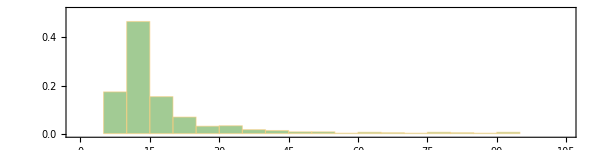

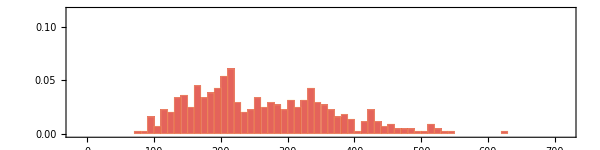

```mathematica
(* This module creates a K-M curve using the given filename *)
date="2019-11-21";
a=makeSurvivalCurve["outputData_1"<>"_"<>date<>".txt"][[1]];
cure={};
progression={};
If[a[[#]]>10000,AppendTo[cure,a[[#]]-10000],AppendTo[progression,a[[#]]]]&/@Range[1,Length[a]];
options={
Frame->{{True,False},{True,False}}
,LabelStyle->{FontSize->18,FontFamily->"Arial"}
,AspectRatio->0.25
,ImageSize->600
,FrameTicks->{{All,None},{All,None}}
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
};
Tf=700;
histCure=Histogram[
cure,35,"Probability",ChartStyle->{Opacity[0.75,ColorData["Rainbow"][0.5]]}
,options
,PlotRange->{{-0.01,1.05}100,{-0.01,1.05}0.49}
]
histProg=Histogram[
progression,40,"Probability",ChartStyle->{Opacity[0.75,ColorData["Rainbow"][0.98]]}
,options
,PlotRange->{{-0.025,1.025}Tf,{-0.01,1.05}0.11}
]
```

```mathematica
Export[NotebookDirectory[]<>"histCure.pdf",histCure,"PDF"]
Export[NotebookDirectory[]<>"histProgression.pdf",histProg,"PDF"]
```

/Users/altrock/Dropbox/Projects_Dropbox/CART/code/hybridModelRuns/histCure.pdf

/Users/altrock/Dropbox/Projects_Dropbox/CART/code/hybridModelRuns/histProgression.pdf

9

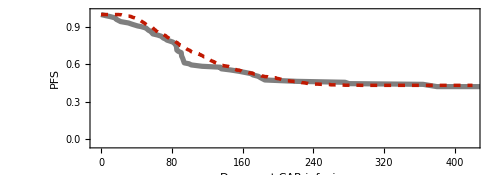

```mathematica
death=Flatten[Import[dir<>"ZUMA1_PFS_death.dat"],0];
L=death//Length;
avMonth=(7 31+28+4*30)/12.;
e=Join[{{0,1}},{death⟦#,1⟧avMonth,death⟦#,2⟧1./100.}&/@Range[1,L,1]];

nStart=4;
nEnd=12;
nFiles = nEnd-nStart+1
date="2019-11-20";

Tf=400;
plotShow[num_,curve_]:=LPsim=ListPlot[(*{rB1[x],rB2[x],rB3[x]},{x,0,Tf},*)
{
e,
{#,curve[[num]][#]}&/@Range[0,1.05Tf,Tf/1000.]
},
Joined->{True,True},
PlotRange->{{-0.01,1.05}Tf ,{-0.05,1.025}},
PlotLegends->Placed[{"",""},{0.45,0.85}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500,
AspectRatio->0.35
,PlotStyle->{
{Thickness[0.0075],Opacity[0.5,Black]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.2]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.6]}
}
]

rBsurvivalCurves=makeSurvivalCurve["outputData_"<>ToString[#]<>"_"<>date<>".txt"]⟦4⟧&/@Range[nStart,nEnd];
plotShow[6,rBsurvivalCurves]
```

```mathematica
nFiles
```

3

```mathematica
Range[4,7]
```

{4,5,6,7}

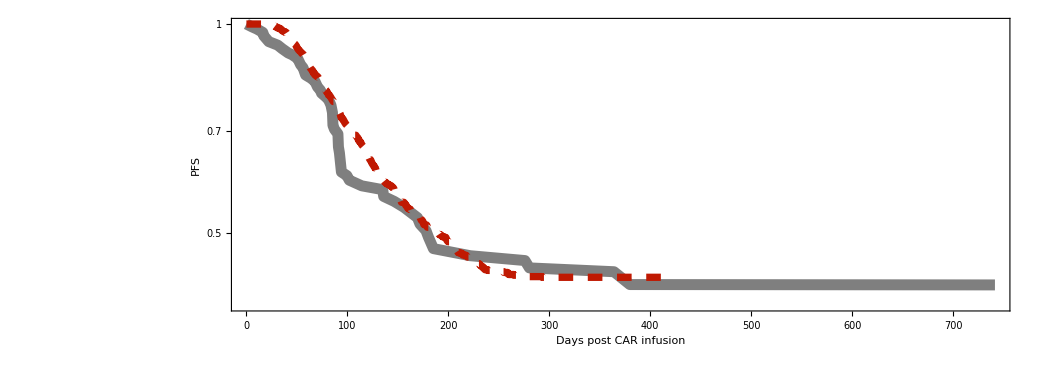

```mathematica
plotShowLog[num_,curve_]:=LPsim=ListLogPlot[(*{rB1[x],rB2[x],rB3[x]},{x,0,Tf},*)
{
e,
{#,curve[[num]][#]}&/@Range[0,1.05Tf,Tf/1000.]
},
Joined->{True,True},
(*PlotRange->{{-0.01,1.05}Tf ,{-0.05,1.025}},*)
PlotLegends->Placed[{"",""},{0.45,0.85}],
Frame->{{True,False},{True,False}},
FrameLabel->{"Days post CAR infusion","PFS"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500,
AspectRatio->0.35
,PlotStyle->{
{Thickness[0.0075],Opacity[0.5,Black]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.2]}
,{Thickness[0.005],,Dashing[{0.01,0.01}],ColorData["SolarColors"][0.6]}
}
]

plotShowLog[6,rBsurvivalCurves]
```